#### Best mean-square approximation polynomial Chebyshev KZ

```mathematica
BMSchebyshev2[n_]:=√(2/Pi)((x+√(x^2-1))^(n+1)-(x-√(x^2-1))^(n+1))/(2 √(x^2-1))
aCoefficient[fun_,n_]:=∫_-1^1 fun*√(1-x^2)*BMSchebyshev2[n]ⅆx
approximant[fun_,n_]:=Sum[N@BMSchebyshev2[k]*aCoefficient[fun,k],{k,0,n}]//FullSimplify
```

#### Discrete function

```mathematica
aCoefD[fun_,list_,n_]:=Sum[fun⟦k⟧*√(1-x^2)*BMSchebyshev2[k]/.x->list⟦k⟧,{k,2,Length@list}]
approximantD[fun_,list_,n_]:=Sum[BMSchebyshev2[k]*aCoefD[fun,list,k],{k,0,n}]//FullSimplify
```

```mathematica
list1=RandomReal[{-1,1},15]//DeleteDuplicates//Sort;
fun1=2#^3+3#^2-6&/@list1;
```

```mathematica
polD=approximantD[fun1,list1,3]//FullSimplify//Expand
```

0.-1.81472 x+3.62945 x^2+7.2589 x^3

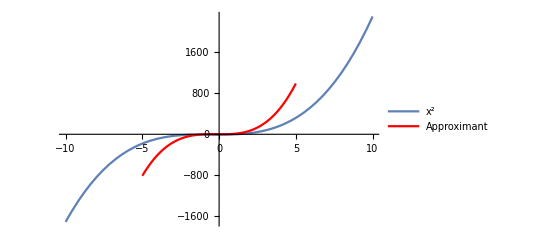

```mathematica
Show[{Plot[2 x^3+3 x^2-6,{x,-10,10},PlotLegends->{"x^2"}],Plot[polD/.x->k,{k,-5,5},PlotStyle->Red,PlotLegends->{"Approximant"}]},PlotRange->Full]
```

```mathematica
list2=RandomReal[{-1,1},20]//DeleteDuplicates//Sort;
```

```mathematica
pol2D=approximantD[Cos[#]&/@list2,list2,4]//Expand
```

3.31945-6.63889 x-26.5556 x^2+26.5556 x^3+53.1112 x^4

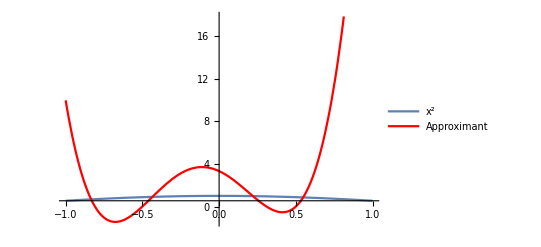

```mathematica
Show[{Plot[Cos[x],{x,-1,1},PlotLegends->{"x^2"}],Plot[pol2D/.x->k,{k,-1,1},PlotStyle->Red,PlotLegends->{"Approximant"}]},PlotRange->Full]
```

#### Test 1

```mathematica
polynomial=approximant[x^2,2]
```

0.+1. x^2

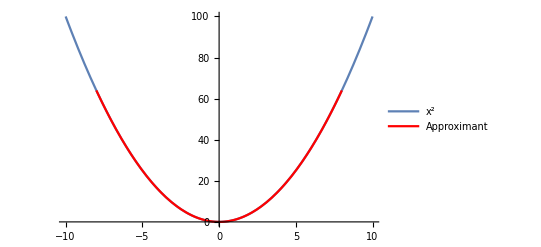

```mathematica
Show[{Plot[x^2,{x,-10,10},PlotLegends->{"x^2"}],Plot[polynomial/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

#### Test 2

```mathematica
polynomial2=approximant[5 x^3+3 x^2-6,3]
```

-6.+x^2 (3.+5. x)

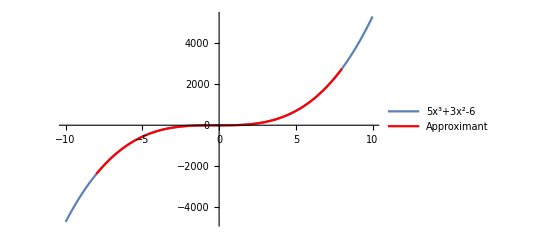

```mathematica
Show[{Plot[5 x^3+3 x^2-6,{x,-10,10},PlotLegends->{"5x^3+3x^2-6"}],Plot[polynomial2/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

#### Test 3

```mathematica
polynomial3=approximant[Sin[x],5]
```

0.999988 x-0.166545 x^3+0.00804032 x^5

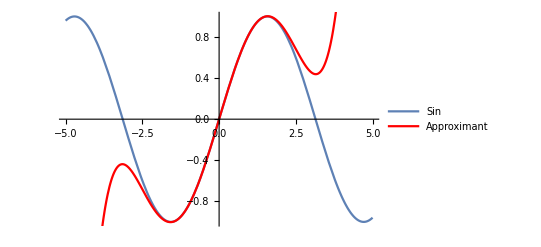

```mathematica
Show[{Plot[Sin[x],{x,-5,5},PlotLegends->{"Sin"}],Plot[polynomial3/.x->k,{k,-5,5},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

#### Recursion

```mathematica
BMSCheb[0]=√(2/Pi);
BMSCheb[1]=2x √(2/Pi);
BMSCheb[n_]:=(2x BMSCheb[n-1]-BMSCheb[n-2])√(2/Pi)
aCoefficient2[fun_,n_]:=∫_-1^1 fun*√(1-x^2)*BMSCheb[n]ⅆx
approximant2[fun_,n_]:=Sum[N@BMSCheb[k]*aCoefficient2[fun,k],{k,0,n}]//FullSimplify
```

```mathematica
pol2=approximant2[5 x^3+3 x^2-6,3]
```

-5.72746+x (1.9368+(1.90986+0.99978 x) x)

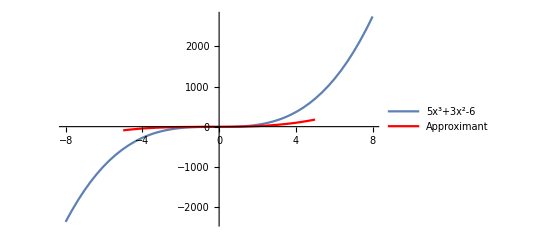

```mathematica
Show[{Plot[5 x^3+3 x^2-6,{x,-8,8},PlotLegends->{"5x^3+3x^2-6"}],Plot[pol2/.x->k,{k,-5,5},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```

```mathematica
pol3=approximant2[Sin[x],3]
```

0.+1.16807 x-0.441727 x^3

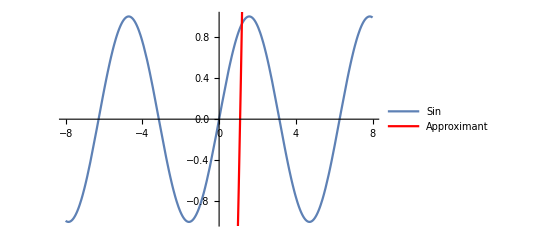

```mathematica
Show[{Plot[Sin[x],{x,-8,8},PlotLegends->{"Sin"}],Plot[pol2/.x->k,{k,-5,5},PlotStyle->Red,PlotLegends->{"Approximant"}]}]
```